# Осциллятор Дуффинга

## 0 Введение

В данной работе проводится качественный анализ поведения нелинейного осциллятора. В качетсве примера был выбран осциллятор, ставший  классической парадигмой для иллюстрации поведения нелинейных систем. Уравнение в общем случае имеет вид:

ẍ+β ẋ+ω x+k x^3=f cos(Ω t)(1)

## 1 Уравние Дюффинга

Рассматривая линейные системы вида

ẍ+β ẋ+ω x=0(2)

можно объяснить лишь узкий спектр явлений происходящих в природе. В общем случае система подчинается нелинейной системе дифференциальных уравнений. Однако важные результаты можно получить и на примере уравнения (2) путем учета зависимости собственной частоты от амплитуды колебаний. Получим:

ẍ+β ẋ+ω x (1+α x^2)=0(3)

Уравнение вида (3) с кубической нелинейностью может описывать, например, математический маятник при небольших углах отклонения, груз и пружину с нелинейной жесткостью, частицу в поле с потенциалом U=1/2 a x^2+ 1/4 b x^4 и т.д.

## 2 Свободные колебания

Начнем анализ с исследования свободной системы, описываемой уравнением

ẍ+β ẋ+ω x +k x^3 =0(4)

Сделаем следующую замену: ẋ=y. Тогда уравнение (4) запишется в виде:

Piecewise[{{ẋ, =   y}, {ẏ, =  -β y-ω x -k x^3}}]

Эта система двух дифференциальных уравнений первого порядка однозначно задает движение осциллятора в момент времени t при заданных начальных условиях. Фазовое пространство представляет собой плоскость.

### 2.1 Положения равновесия

Положения равновесия определятся следующей системой алгебраических уравнений:

Piecewise[{{0, =   y}, {0, =  β y+ω x +k x^3}}]

Решая данную систему уравнений, получаем:

P_1:   {x=0, y=0}
P_2:   {x=i √(ω/k), y=0}
P_3:   {x=-i √(ω/k), y=0}(4)

Заметим, что три положения равновесия существуют лишь тогда, когда ω и k будут разных знаков. При стремлении значений параметра κ к нулю (переход к линейному осциллятору) точки P_2 и P_3 уходят в ±∞ и остается только одно положение равновесия.

Поясним выше сказанное на примере консервативной системы с уравнением:

ẍ+ω x + x^3 =0

Ей соответствует гамильтониан вида: H = v^2/2+ω u^2/2+u^4/4. Поскольку решения лежат на линиях уровня H, изобразим фазовый портрет:

```mathematica
list1=Range[-0.20,-0.16,0.05];
list2=Range[0,0.9,0.2];
list =Join[list1, list2];
Manipulate[
graph1 = ContourPlot[v^2/2+ω*u^2/2+u^4/4==list,  {u, -4, 4}, {v, -4, 4},PlotRange->All, AspectRatio->3/4, ImageSize->400, PlotPoints->50, PlotLabel->"Рис.1: Фазовый портрет консервативной системы. k=1"];
graph2 = Graphics[{
PointSize[Large],Red,
Point[{
{0,0},
{Re[I √(ω/1)], 0},
{Re[-I √(ω/1)], 0}
}]
}];

Show[{graph1}, graph2],
{{ω,-1, "Соб. частота, ω"}, -5, 5, Appearance->"Labeled"}, SaveDefinitions->True
]
```

### 2.2 Характер положений равновесия

Исследуем характер пложений равновесия следующей системы в зависимости от параметров осциллятора:

Piecewise[{{ẋ, =   y}, {ẏ, =  -β y-ω x -k x^3}}]

Для решения поставленной задачи последовательно линеаризуем систему в окрестности каждого из положений равновесия P_1 и P_2 (P_3 аналогично):

P_1:Piecewise[{{ẋ, =   y}, {ẏ, =  -ω x -β y}}]
P_2:Piecewise[{{u̇, =  v}, {v̇, =  2ω u- β v}}]

Где u = x - i √(ω/k), v = y. Корни характеристического урвнения имеют вид:

P_1:   λ_(1,2)^1=-β/2±√(β^2/4-ω)
P_2:  λ_(1,2)^2=-β/2±√(β^2/4+2ω)

Рассмотрим только грубые положения равновесия (поведение фазовых траеторий в окрестности грубого положения равновесия качественно совпдает с поведением фазовых траекторий линеаризованной системы в этой точке).

Случай А: Sign(ω k)>0

Существует только одно положение равновесия в соответствие с (4).
I) k<0, ω<0
Re(λ_1^1)>0, Re(λ_2^1)<0 ⇒ положение равновесия типа седло. Рассуждение справедливо для любых β.

```mathematica
Manipulate[
graph3=StreamPlot[{y,β*y+1*x+1* x^3},{x,-1,1},{y,-1,1},AspectRatio->3/4,ImageSize->300, PlotLabel->"Рис.2: w=k=-1"];
graph4=Graphics[{
PointSize[Large],Red,
Point[{0,0}]
}];
Show[{graph3}, graph4],

{{β,-1,  "Коэф. затухания, β"},-2,2,Appearance->"Labeled"}
]
```

II) k>0, ω>0
β∈(-∞,-2 √ω) - неустойчивый узел
β∈(-2 √ω, 0) - неустойчивый фокус
β∈(0,2 √ω) - устойчивый фокус
β∈(2 √ω, +∞,) - устойчивый узел

```mathematica
Manipulate[
graph5=StreamPlot[{y,-β*y-1*x-1* x^3},{x,-1,1},{y,-1,1},AspectRatio->3/4,ImageSize->300, PlotLabel->"Рис.3: w=k=1"];
graph6=Graphics[{
PointSize[Large],Red,
Point[{0,0}]
}];
If[β<-2,graph7=Graphics[Text[Style["Неустойчивый узел", Red, Bold, 14],{0.5,0.8}]], ];
If[-2<β<0,graph7=Graphics[Text[Style["Неустойчивый фокус", Red, Bold, 14],{0.5,0.8}]], ];
If[0<β<2,graph7=Graphics[Text[Style["Устойчивый фокус", Red, Bold, 14],{0.5,0.8}]], ];
If[β>2,graph7=Graphics[Text[Style["Устойчивый узел", Red, Bold, 14],{0.5,0.8}]], ];

Show[graph5, graph6, graph7],

{{β,-2.5,  "Коэф. затухания, β"},-3,3,Appearance->"Labeled"}
]
```

Случай Б: Sign(ω k)<0

Существует 3 положения равновесия в соответствии с (4).
I) k<0, ω>0

β∈(-∞,-2 √ω):Piecewise[{{P_1, :  неустойивый узел}, {P_2, :  седло}}]
	β∈(-2 √ω,0):Piecewise[{{P_1, :  неустойчивый фокус}, {P_2, :  седло}}]
		β∈(0,2 √ω):Piecewise[{{P_1, :  устойчивый фокус}, {P_2, :  седло}}]
			β∈(2 √ω,+∞):Piecewise[{{P_1, :  устойчивый узел}, {P_2, :  седло}}]

```mathematica
Manipulate[
graph8=StreamPlot[{y,-β*y-1*x+1* x^3},{x,-2,2},{y,-2,2},AspectRatio->3/4,ImageSize->300, PlotLabel->"Рис.3: w=1, k=-1"];
graph9 = Graphics[{
PointSize[Large],Red,
Point[{
{0,0},
{Re[I √-1], 0},
{Re[-I √-1], 0}
}]
}];
If[β<-2,graph10=Graphics[Text[Style["Неустойчивый узел", Red, Bold, 14],{1.0,1.8}]], ];
If[-2<β<0,graph10=Graphics[Text[Style["Неустойчивый фокус", Red, Bold, 14],{1.0,1.8}]], ];
If[0<β<2,graph10=Graphics[Text[Style["Устойчивый фокус", Red, Bold, 14],{1.0,1.8}]], ];
If[β>2,graph10=Graphics[Text[Style["Устойчивый узел", Red, Bold, 14],{1.0,1.8}]], ];

l1=Line[{{0.1,0.18}, {0.9,1.62}}];
graph11=Graphics[{Red,Thick,l1}];

l2=Line[{{-1.0,-0.18}, {-0.9,-1.62}}];
graph12=Graphics[{Red,Thick,l2}];

graph13=Graphics[Text[Style["Седла", Red, Bold, 14],{-1.0,-1.8}]];

Show[graph8, graph9, graph10, graph11, graph12, graph13],

{{β,-2.5,  "Коэф. затухания, β"},-3,3,Appearance->"Labeled"}
]
```

II) k>0, ω<0

β∈(-∞,-2 √(2ω)):Piecewise[{{P_1, :  неустойчивый узел}, {P_2, :  седло}}]
	β∈(-2 √(2ω),0):Piecewise[{{P_1, :  неустойчивый фокус}, {P_2, :  седло}}]
		β∈(0,2 √(2ω)):Piecewise[{{P_1, :  устойчивый фокус}, {P_2, :  седло}}]
			β∈(2 √(2ω),+∞):Piecewise[{{P_1, :  устойчивый узел}, {P_2, :  седло}}]

Рисунок в целом аналогичный предыдущему пункту.

## 3 Вынужденные колебания

### 3.1 Фазовое пространство

Вернемся к уравнению (1), положив в нем β=0.1, ω=-1, k=1, Ω=1.4, f=0.1. Получим:

ẍ+0.1 ẋ-x+ x^3=0.1 cos(1.4 t)

Численно решим это уравение и построим фазовый портрет:

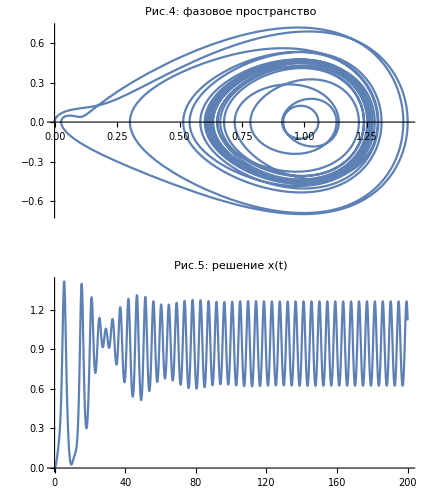

```mathematica
(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;f=0.1;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]+ω*x[t]+k*x[t]^3==f*Cos[Ω*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==0,
x'[0]==0
};

(* -------------------- Solution ------------------- *)
solution = NDSolve[ { deqns, incs },{ x[t], x'[t] }, { t, 0,800}, MaxSteps->Infinity];

(* -------------- Graph 1: Phase Space ------------- *)
graph20=ParametricPlot[ 
{ x[t]/.solution[[1]],x'[t]/.solution[[1]] },
{t, 0,200},
 PlotLabel->Style["Рис.4: фазовое пространство"(*,FontSize->16*)],
ImageSize->400, AspectRatio-> 9/16, PlotPoints-> 1000
];

(* --------------- Graph 2: Solution -------------- *)
graph21=Plot[ 
x[t]/.solution[[1]],
{t, 0,200},
 PlotLabel->Style["Рис.5: решение x(t)"(*,FontSize->16*)],
ImageSize->400, AspectRatio-> 9/16, PlotPoints-> 1000
];

GraphicsGrid[  {{graph20},{graph21}} ]
```

Фазовое пространство выглядит достаточно сложным, однако оно также включает в себя и процесс затухания собственных колебаний. Как видно из Рис.5 они затухают на временах ~100. Построим фазовый портрет на промежутке веремени от 200 до 250, напимер:

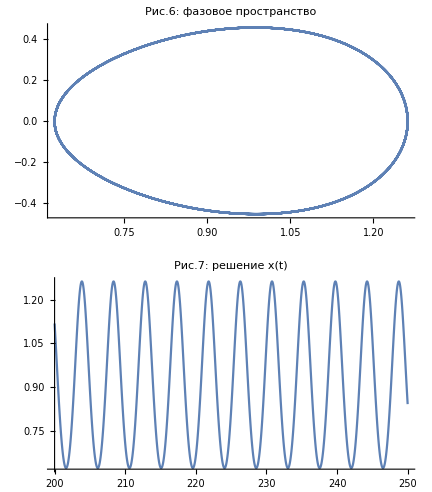

```mathematica
(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;f=0.1;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]+ω*x[t]+k*x[t]^3==f*Cos[Ω*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==0,
x'[0]==0
};

(* -------------------- Solution ------------------- *)
solution = NDSolve[ { deqns, incs },{ x[t], x'[t] }, { t, 0,800}, MaxSteps->Infinity];

(* -------------- Graph 1: Phase Space ------------- *)
graph20=ParametricPlot[ 
{ x[t]/.solution[[1]],x'[t]/.solution[[1]] },
{t, 200,250},
 PlotLabel->Style["Рис.6: фазовое пространство"(*,FontSize->16*)],
ImageSize->400, AspectRatio-> 9/16, PlotPoints-> 1000
];

(* --------------- Graph 2: Solution -------------- *)
graph21=Plot[ 
x[t]/.solution[[1]],
{t, 200,250},
 PlotLabel->Style["Рис.7: решение x(t)"(*,FontSize->16*)],
ImageSize->400, AspectRatio-> 9/16, PlotPoints-> 1000
];

GraphicsGrid[  {{graph20},{graph21}} ]
```

Фазовая траектория стала заметно проще и представляет собой предельный цикл. Не представляет труда проверить, что период равен (2π)/ω.

```mathematica
Manipulate[
(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;f=0.1;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]-x[t]+x[t]^3==f*Cos[1.4*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==0,
x'[0]==0
};

(* -------------------- Solution ------------------- *)
solution = NDSolve[ { deqns, incs },{ x[t], x'[t] }, { t, 0,300}, MaxSteps->Infinity];

(* -------------- Graph 1: Phase Space ------------- *)
graph22=ParametricPlot[ 
{ x[t]/.solution[[1]],x'[t]/.solution[[1]] },
{t, 200,tmax},
 PlotLabel->Style["Рис.8: фазвое пространство"(*,FontSize->16*)],
ImageSize->300, AspectRatio-> 9/16,
PlotRange->{{.6,1.3},{-0.5,0.5}}
];

(* --------------- Graph 2: Solution -------------- *)
graph23=Plot[ 
x[t]/.solution[[1]],
{t, 200,tmax},
 PlotLabel->Style["Рис.9: решение x(t)"(*,FontSize->16*)],
ImageSize->300, AspectRatio-> 9/16,
PlotRange->{{200,210},{.6,1.3}}
];

GraphicsGrid[  {{graph22},{graph23}} ],

{{tmax,204,"t"},200.1,210,Appearance->"Labeled"}
]
```

### 3.2 Удвоение периода

Исследуем поведение системы в зависимости от амплитуды вынужденных колебаний. Все графики будут приведены для времен, когда собственные колебания практически затухли.

Увеличим амплитуду вынужденных колебаний с f = 0.1 до f=0.32. Получим:

```mathematica
Manipulate[
(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;f=0.32;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]-x[t]+x[t]^3==f*Cos[1.4*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==0,
x'[0]==0
};

(* -------------------- Solution ------------------- *)
solution = NDSolve[ { deqns, incs },{ x[t], x'[t] }, { t, 0,300}];

(* -------------- Graph 1: Phase Space ------------- *)
graph24=ParametricPlot[ 
{ x[t]/.solution[[1]],x'[t]/.solution[[1]] },
{t, 200,tmax},
 PlotLabel->Style["Рис.8: фазвое пространство"(*,FontSize->16*)],
ImageSize->300, AspectRatio-> 9/16,
PlotRange->{{-1.4, -.1},{-.7,.7}}
];

(* --------------- Graph 2: Solution -------------- *)
graph25=Plot[ 
x[t]/.solution[[1]],
{t, 200,tmax},
 PlotLabel->Style["Рис.9: решение x(t)"(*,FontSize->16*)],
ImageSize->300, AspectRatio-> 9/16,
PlotRange->{{200, 220},{-1.4,-.2}}
];

(*graph26 = Graphics[{
PointSize[Large],Red,
Point[{
{Extract[x[tmax]/.solution[[1]],1],Extract[x[tmax]/.solution[[1]],1]}
}]
}];*)

(*GraphicsGrid[  {{Show[graph24, graph26]},{graph25}} ],*)

GraphicsGrid[  {{graph24},{graph25}} ],

{{tmax,208,"t"},200.1,220,Appearance->"Labeled"}
]
```

И на фазовом пространстве и на графике решения хорошо видно, что произошло удвоение периода. Теперь он равен (4π)/ω. Еще раз увеличим амплитуду вынужденных колебаний с f = 0.32 до f=0.338. Получим:

```mathematica
Manipulate[
(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;f=0.338;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]-x[t]+x[t]^3==f*Cos[1.4*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==0,
x'[0]==0
};

(* -------------------- Solution ------------------- *)
solution = NDSolve[ { deqns, incs },{ x[t], x'[t] }, { t, 0,1100}];

(* -------------- Graph 1: Phase Space ------------- *)
graph24=ParametricPlot[ 
{ x[t]/.solution[[1]],x'[t]/.solution[[1]] },
{t, 1000,tmax},
 PlotLabel->Style["Рис.10: фазвое пространство"(*,FontSize->16*)],
ImageSize->300, AspectRatio-> 9/16,
PlotRange->{{-1.4, -.1},{-.7, .7}}
];

(* --------------- Graph 2: Solution -------------- *)
graph25=Plot[ 
x[t]/.solution[[1]],
{t, 1000,tmax},
 PlotLabel->Style["Рис.11: решение x(t)"(*,FontSize->16*)],
ImageSize->300, AspectRatio-> 9/16,
PlotRange->{{1000, 1030},{-1.4,-.1}}
];

(*graph26 = Graphics[{
PointSize[Large],Red,
Point[{
{0,-1}
}]
}];*)

(*GraphicsGrid[  {{Show[graph24, graph26]},{graph25}} ],*)

GraphicsGrid[  {{graph24},{graph25}} ],

{{tmax,1010,"t"},1000.1,1040,Appearance->"Labeled"}
]
```

InterpolatingFunction::dmval: Input value {1000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

И снова произошло удвоение периода.

### 3.3 Сечение Пуанкаре

При дальнейшем увеличении амплитуды вынуждающей силы такой спосб изучения не слишком практичен. Удобно строить сечение Пуанкаре, которое представляет собой отображение положения системы в моменты времени t_0, t_0+T, t_0+2T... Понятно, что при удвоении периода вместо одной точки на вазовой диаграмме появятся две и т.д.

Сечение Пуанкаре для предыдущего случая ( f=0.338 ) выглядит следующим образом:

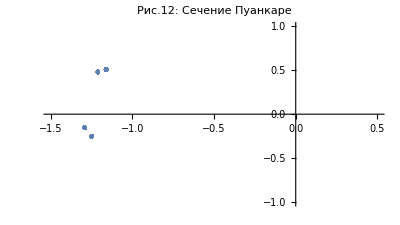

```mathematica
(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;f=0.338;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]+ω*x[t]+k*x[t]^3==f*Cos[Ω*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==0,
x'[0]==0
};

points=Reap[
NDSolve[
{deqns,incs},
{},
{t,0,10000},MaxSteps->Infinity,
Method->{
"EventLocator","Event"->Mod[t,2π/1.4],
"EventAction":>Sow[{x[t],x'[t]}]
}
]
];

points = points[[2]];
points = points[[1]];

ListPlot[
Drop[points,300],
PlotLabel->Style["Рис.12: Сечение Пуанкаре"(*,FontSize->16*)],
ImageSize->400, AspectRatio-> 9/16,
PlotRange->{{-1.5,0.5},{-1.0,1.0}},
PlotStyle->PointSize[Large]]
```

При f=0.35:

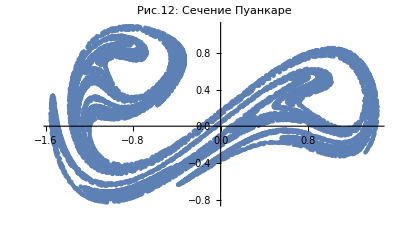

```mathematica
(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;f=0.35;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]+ω*x[t]+k*x[t]^3==f*Cos[Ω*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==0,
x'[0]==0
};

points=Reap[
NDSolve[
{deqns,incs},
{},
{t,0,100000},MaxSteps->Infinity,
Method->{
"EventLocator","Event"->Mod[t,2π/1.4],
"EventAction":>Sow[{x[t],x'[t]}]
}
]
];

points = points[[2]];
points = points[[1]];

ListPlot[
Drop[points,300],
PlotLabel->Style["Рис.12: Сечение Пуанкаре"(*,FontSize->16*)],
ImageSize->400, AspectRatio-> 9/16,
PlotRange->All,
PlotStyle->PointSize[Small]]
```

### 3.4 Бифуркационная диаграмма

Бифуркационная диаграмма. f изменяется от f=0.30 до f=0.342 с шагом 0.00001.

```mathematica
ListPlot[
Flatten[
Table[

{

(* ------------------- Input Data ------------------ *)
m=1;β =0.1;ω=-1; k=1;Ω=1.4;

(* ------------- Differential Equations ------------ *)
deqns = {
m*x''[t] + β*x'[t]+ω*x[t]+k*x[t]^3==f*Cos[Ω*t]
};

(* --------------- Initial Conditions -------------- *)
incs = {
x[0]==1,
x'[0]==0
};

points=Reap[
NDSolve[
{deqns,incs},
{},
{t,0,5000},MaxSteps->Infinity,
Method->{
"EventLocator","Event"->Mod[t,2π/1.4],
"EventAction":>Sow[{f,x[t]}]
}
]
];

points = points[[2]];
points = points[[1]];
points=Drop[points,900]

}
,

{f,0.3,0.342,0.00001}
],2
],
ImageSize->Large
]
```

-Graphics-